# Alternative Output Formatting

Date: March 30, 2017

The following code provides automatic printing of both input and output, in TraditionalForm, as well as easy in-line combination of text and math.

The code changes the standard Mathematica format for output, and this change remains in effect until one deactivates the code, quits the kernel, or quits Mathematica.  To deactivate the code, paste the following into a cell and evaluate it:

$PreRead=.
$PrePrint=.

This code was created by the collaborative work of MSE members Mr.Wizard, Simon Rochester, MB1965, and myself, Aron Yoffe.  Attribution:
•Mr. Wizard: Provided the code that prints text and output on the same line, and subsequently added code that directs any graphical output to be printed on its own line (immediately after the line on which the input code is printed), and code that allows one to suppress the automatic printing of input for individual commands (by terminating that command with a triple semicolon—see below). Did bug fixes.
•Simon Rochester: Provided the code that automatically prints input and output on the same line.  Did bug fixes.
•MB1965: Merged Simon Rochester’s code block with Mr. Wizard’s initial code block (both codes contained $PrePrint statements; these had to be merged into a single combined $PrePrint statement, since only one $PrePrint statement can be active at a time), and rewrote and improved the text formatting code.  Did bug fixes.
•Aron Yoffe: Provided the initial idea to create this code, guided its development through a series of posts on MSE, decided what functionality and features it should offer, improved the text formatting of Mr. Wizard’s code, did bug fixes, and was responsible for bug identification and testing.

```mathematica
$PreRead=.
$PrePrint=.

$note1=Null;
$note2=Null;
$note3=Null;

$outputStyles=<|"Default"->{Blue,15,Italic,FontFamily->"Times"},"Before"->{Blue,15,Italic,FontFamily->"Times"},"After"->{Blue,15,Italic,FontFamily->"Times"}|>;

boxExpr[body_]:=RowBox@{"Replace","[","\"thisIsJustATag\"",";",body,",","Null","->","\"\"","]"};
styleNote[note_,style_]:=Style[ToExpression@note,Sequence@@Lookup[$outputStyles,style,$outputStyles["Default"]]];

extractNotes[boxes_]:=Replace[boxes,{RowBox[{note1_String?(StringMatchQ[#,"\"*\""]&),";",body__,";",note2_String?(StringMatchQ[#,"\"*\""]&)}]:>($note1=styleNote[note1,"Before"];$note2=styleNote[note2,"After"];
boxExpr@body),RowBox[{body__,";",note_String?(StringMatchQ[#,"\"*\""]&)}]:>($note2=styleNote[note,"After"];
$note1=Null;
boxExpr@body),RowBox[{note_String?(StringMatchQ[#,"\"*\""]&),";",body__}]:>($note1=styleNote[note,"After"];
$note2=Null;
boxExpr@body),RowBox[{note_String?(StringMatchQ[#,"\"*\""]&),";"}]:>($note3=styleNote[note,"Neither"];
$note2=Null;$note1=Null;
note),e_:>($note1=Null;$note2=Null;boxExpr@e)}];

applyFormatting[out_]:=With[{line=$Line},HoldForm[In[line]=$placeHolder]/.DownValues[In]/.{$placeHolder->out,HoldPattern[Replace[CompoundExpression["thisIsJustATag",expr_],Null->""]]:>expr}/.{HoldPattern[a_=""]:>a,HoldPattern[a_=a_]:>a,HoldPattern[a_=HoldForm[a_]]:>a,HoldPattern[(c:(a_=b_))=b_]:>c,HoldPattern[(a_=b_)=c_]:>HoldForm[a=b=c]}];
addNotes[formatted_]:=TraditionalForm@Switch[{$note1,$note2,$note3},{Null,Null,Except@Null},With[{r=$note3},$note3=Null;r],{Except@Null,Except@Null,_},With[{r1=$note1,r2=$note2},$note1=$note2=Null;
Row[{r1,formatted,r2},Spacer[5]]],{Except@Null,_,_},With[{r=$note1},$note1=Null;
Row[{r,formatted},Spacer[5]]],{_,Except@Null,_},With[{r=$note2},$note2=Null;
Row[{formatted,r},Spacer[5]]],_,formatted];

bypass=Replace[RowBox[{b1___,RowBox[{b2___,";;"}],";"}]:>($bypass=True;RowBox[{b1,b2}])];

applyFormatting[out_]/;$bypass:=Pane[out];

self:addNotes[formatted_]/;$bypass:=($bypass=.;
Unevaluated[self]/.(DownValues[addNotes]/.Row->Column))

SetAttributes[graphicsQ,HoldFirst]

graphicsQ[_Graphics|_Graphics3D|_Graph|_Image|_Image3D]=True;
graphicsQ[Legended[_?graphicsQ,___]]=True;
graphicsQ[{___,_?graphicsQ,___}]=True;

applyFormatting[out_?graphicsQ]:=Column[{#/.DownValues[In],Pane@out}]&[HoldForm@TraditionalForm@In@#&@$Line]/.HoldPattern[Replace["thisIsJustATag";expr_,Null->""]]:>expr

$PreRead=extractNotes@*bypass;
$PrePrint=addNotes@*applyFormatting;
```

$PrePrint=addNotes@*applyFormatting;

Automatic in-line printing of both input and output, in TraditionalForm:

```mathematica
α=Integrate[x^2, x]
β=Sum[1/p^2,{p,1,Infinity}]
g[x_]:=Sin[x]
Table[100i+10j+k,{i,3},{j,2},{k,4}]
```

α=∫x^2 ⅆx=x^3/3

β=∑_(p=1)^∞ 1/p^2=π^2/6

g(x_):=sin(x)

Table[100 i+10 j+k,{i,3},{j,2},{k,4}]=({111,112,113,114} | {121,122,123,124}
{211,212,213,214} | {221,222,223,224}
{311,312,313,314} | {321,322,323,324})

Text can be easily added by placing it in quotes and separating it from the math with a semicolon, either before or after the math, or both.  One can also enter text alone (note that the latter must be terminated with a semicolon):

```mathematica
"We define α as follows:"; α=Integrate[x^2, x]
β=Sum[1/p^2,{p,1,Infinity}];", giving us the same result we calculated using the first method."
"Here we define the function";g[x_]:=Sin[x];"using a delayed assignment."
"We can place the text on its own line by adding a hard return just before the closing quote:
";Table[100i+10j+k,{i,3},{j,2},{k,4}]
"Just some text by itself";
```

We define α as follows:α=∫x^2 ⅆx=x^3/3

β=∑_(p=1)^∞ 1/p^2=π^2/6, giving us the same result we calculated using the first method.

Here we define the functiong(x_):=sin(x)using a delayed assignment.

We can place the text on its own line by adding a hard return just before the closing quote:
Table[100 i+10 j+k,{i,3},{j,2},{k,4}]=({111,112,113,114} | {121,122,123,124}
{211,212,213,214} | {221,222,223,224}
{311,312,313,314} | {321,322,323,324})

Just some text by itself

Further, by using this handy code-hiding palette, developed by MSE member R. M. (see second answer at http://mathematica.stackexchange.com/questions/14466/is-there-a-way-to-hide-or-toggle-the-visibility-of-code), one can hide all the input code, leaving only the math+text output seen above.  Used together, these two code blocks (the alternative output formatting code and the code-hiding palette) semi-automate the production of documents that will be non-cryptic to those unfamiliar with Mathematica syntax.  Note the purpose here is not to produce publication-quality output, but rather to minimize the effort needed to create documents (e.g., solution sets for students, draft calculations for colleagues, etc.) that can be understood by non-Mathematica users. 

To distribute the finished document, select “Hide code”, save the notebook, close it, and then reopen it.  That cleans it up by removing all the input and output cell numbering.  Then you can save it as a .pdf, enabling those that don’t have access to Mathematica to read it.

```mathematica
CreatePalette[Column[{Button["Hide code",{NotebookFind[SelectedNotebook[],"Output",All,CellStyle];
FrontEndExecute[FrontEndToken[SelectedNotebook[],"SelectionCloseUnselectedCells"]]}],Button["Show code",NotebookFind[SelectedNotebook[],"Input",All,CellStyle]]}]]
```

CreatePalette[Hide code
Show code]=d3na8_shm114FrontEndObject[LinkObject["d3na8_shm", 3, 1]]114Untitled-19

In-line output of graphics would result in overly small figures.  Thus, for all commands with graphical output, the output is automatically placed on a separate line:

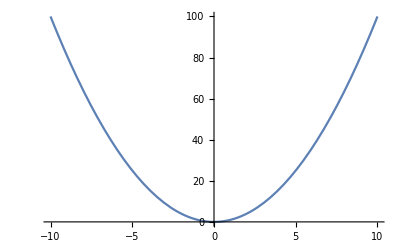
Plot[x^2,{x,-10,10}]
-Graphics-

```mathematica
Plot[x^2, {x,-10,10}]
```

Terminating the input with a semicolon retains its normal effect of eliminating the output—thus only the input is printed:

```mathematica
α=Integrate[x^2, x];
β=Sum[1/p^2,{p,1,Infinity}];
g[x_]:=Sin[x];
Table[100i+10j+k,{i,3},{j,2},{k,4}];
γ=RandomReal[1,10^5];
```

α=∫x^2 ⅆx;

β=∑_(p=1)^∞ 1/p^2;

g(x_):=sin(x);

Table[100 i+10 j+k,{i,3},{j,2},{k,4}];

γ=RandomReal[1,10^5];

For most commands (except those using assignments or Postfix; see Issue #2, below), one can suppress the printing of input by terminating the command with a triple semicolon (;;;).  Doing so causes the output to revert to its default appearance:

x^3/3

π^2/6

({111,112,113,114} | {121,122,123,124}
{211,212,213,214} | {221,222,223,224}
{311,312,313,314} | {321,322,323,324})

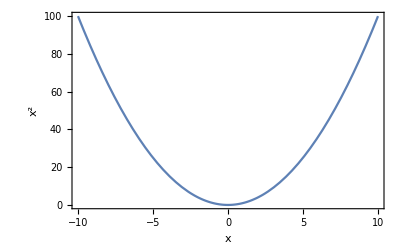

```mathematica
Integrate[x^2, x];;;
Sum[1/p^2,{p,1,Infinity}];;;
Table[100i+10j+k,{i,3},{j,2},{k,4}];;;
Plot[x^2, {x,-10,10}, LabelStyle->Directive[Black,FontFamily->"Times",18],Frame->True,FrameLabel->{Style["x",Italic],Style["x^2", Italic]}];;;
```

Even if the triple semicolon is used to suppress the printing of input, the text-insertion portion of the code still works (but only if the text is placed before the math).   For instance, suppose we added extra specifications to the above Plot command, making the input too cryptic to serve as a plot title (see first example, below).  In that case, we might want to title the plot manually with text alone, as is done here (see second example; note the hard return just before the closing quote, which forces the graphic to be on the line after the text):

```mathematica
Plot[x^2, {x,-10,10}, LabelStyle->Directive[Black,FontFamily->"Times",18],Frame->True,FrameLabel->{Style["x",Italic],Style["x^2", Italic]}]
"A plot of x^2 vs. x
";Plot[x^2, {x,-10,10}, LabelStyle->Directive[Black,FontFamily->"Times",18],Frame->True,FrameLabel->{Style["x",Italic],Style["x^2", Italic]}];;;
```

Plot[x^2,{x,-10,10},LabelStyle→Directive[Black,FontFamily→Times,18],Frame→True,FrameLabel→{x,x^2}]
-Graphics-

A plot of x^2 vs. x

-Graphics-

Alternately, one could instead title the plot with PlotLabel, and use the text-alone option to add a caption below the plot.  [A better result can be achieved with Grid, but this approach is much simpler to implement.]:

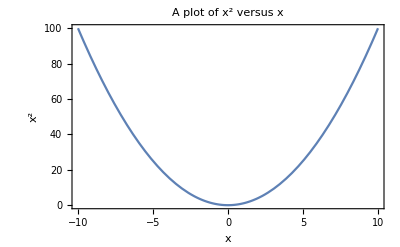

Fig. 5. One can easily add a detailed caption below the plot, such as this,
controlling the length of the lines (if desired) with hard returns, as I've
done here.  Or one can let the program wrap the lines.

```mathematica
Plot[x^2, {x,-10,10}, LabelStyle->Directive[Black,FontFamily->"Times",18],Frame->True,FrameLabel->{Style["x",Italic],Style["x^2", Italic]},PlotLabel->"A plot of x^2 versus x"];;;
"Fig. 5. One can easily add a detailed caption below the plot, such as this,
controlling the length of the lines (if desired) with hard returns, as I've
done here.  Or one can let the program wrap the lines.";
```

ISSUES

1) It doesn’t work with the Graphics and Graphics3D commands—the input is printed as a graphic instead of as text.  In addition, there is sometimes an error message :

-Graphics3D-
-Graphics3D-

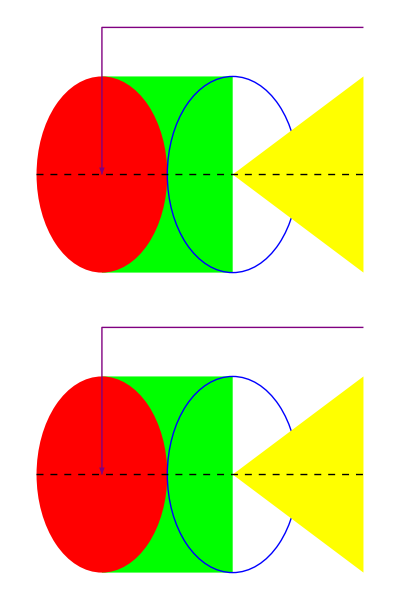

```mathematica
Graphics3D[Cylinder[]]
Graphics[{Thick,Green,Rectangle[{0,-1},{2,1}],Red,Disk[],Blue,Circle[{2,0}],Yellow,Polygon[{{2,0},{4,1},{4,-1}}],Purple,Arrowheads[Large],Arrow[{{4,3/2},{0,3/2},{0,0}}],Black,Dashed,Line[{{-1,0},{4,0}}]}]
```

2) The command to suppress printing of input (;;;) doesn't work with assignments and Postfix:

```mathematica
α=Integrate[x^2, x];;;
g[x_]:=Sin[x];;;
Sin[x]//N;;;
```

α=∫x^2 ⅆx;;All;

g(x_):=sin(x);;All;

(N;;All)(sin(x));

3) There are two issues associated with the use of a semicolon to suppress output:

a) It doesn’t work with text:

```mathematica
"Some text";Integrate[x^2,x];
```

b) With commands that give graphical output (e.g., Plot), the system sometimes prints the semicolon in red, even though the functionality is unaffected.  [If you see a red semicolon, it will revert to black as soon as you quit the kernel and thus deactivate the code.]